```mathematica
(* ====== Guinea ====== *)
ClearAll[n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];
n=10057975;
Udata = {1585,1616,1648,1642,1649,1630,1636,1639,1756,1867,1844,1810,1790,1763,1744,1485,1218,1226,1234,1246,1259,1253,1276,1210,1232,1268,1286,1242,1206,1293,1292,1258,1204,1164,1214,1267,1275,1275,1344,1420,1490,1500,1507,1353,1191,1258,1300,1364,1346,1342,1279,1199,1217,1246,1266,1224,1223,1174,1183,1147,1114,1794,1763,1880,1113,1125,1133,1149,1156,1132,1138,1123,1916,1123,1150,1188,1161,1163,1186,1138,1174,1203,1240,1204,1208,1181}
Mdata = {208,208,208,208,209,209,210,210,213,213,215,215,214,211,210,210,210,210,210,210,210,210,210,215,215,216,216,221,221,229,229,229,263,263,263,263,263,263,263,263,263,263,263,266,269,269,273,275,275,276,276,276,277,279,280,282,282,282,282,283,283,284,284,284,284,288,298,298,319,319,319,319,319,323,328,332,332,332,332,332,335,339,342,347,347,347}
Adata = {1612,1630,1647,1657,1667,1678,1688,1698,1722,1745,1766,1787,1808,1829,1850,1871,1892,1902,1911,1921,1929,1929,1949,1956,1982,2009,2035,2043,2051,2081,2096,2102,2109,2115,2121,2127,2146,2164,2196,2227,2259,2284,2284,2313,2342,2356,2370,2384,2397,2397,2416,2435,2445,2455,2465,2471,2471,2477,2493,2498,2503,2508,2508,2514,2522,2525,2530,2534,2539,2539,2539,2542,2545,2550,2554,2559,2569,2569,2571,2575,2581,2587,2593,2608,2608,2621}
Ddata = {1142,1154,1166,1171,1176,1182,1187,1192,1203,1214,1223,1232,1242,1251,1260,1272,1284,1293,1303,1312,1327,1327,1349,1366,1381,1397,1412,1420,1428,1454,1462,1481,1499,1518,1522,1525,1538,1550,1562,1574,1586,1607,1607,1631,1654,1668,1683,1697,1708,1709,1724,1739,1748,1758,1767,1781,1781,1786,1797,1800,1804,1807,1807,1814,1821,1829,1844,1860,1875,1876,1876,1879,1880,1889,1897,1906,1910,1910,1911,1913,1921,1929,1937,1944,1944,1947}
Sdata = {10054985,10054942,10054910,10054895,10054881,10054870,10054856,10054843,10054802,10054767,10054737,10054710,10054672,10054648,10054621,10054594,10054568,10054548,10054528,10054508,10054484,10054484,10054440,10054417,10054374,10054327,10054284,10054267,10054255,10054182,10054159,10054138,10054084,10054063,10054048,10054034,10054001,10053971,10053920,10053879,10053838,10053791,10053791,10053730,10053681,10053657,10053619,10053583,10053561,10053559,10053532,10053496,10053484,10053459,10053437,10053419,10053419,10053403,10053375,10053370,10053364,10053349,10053349,10053335,10053327,10053311,10053280,10053259,10053217,10053218,10053218,10053213,10053202,10053191,10053171,10053150,10053138,10053138,10053133,10053132,10053111,10053090,10053069,10053046,10053046,10053032}
ϵ=Sum[(Udata[[i+1]]-Udata[[i]]+p*Udata[[i]]-x/n*Sdata[[i]]*(Mdata[[i]]+Adata[[i]]))^2,{i,Length@Udata-1}]
N@Minimize[ϵ,{x,p}]
```

{1585,1616,1648,1642,1649,1630,1636,1639,1756,1867,1844,1810,1790,1763,1744,1485,1218,1226,1234,1246,1259,1253,1276,1210,1232,1268,1286,1242,1206,1293,1292,1258,1204,1164,1214,1267,1275,1275,1344,1420,1490,1500,1507,1353,1191,1258,1300,1364,1346,1342,1279,1199,1217,1246,1266,1224,1223,1174,1183,1147,1114,1794,1763,1880,1113,1125,1133,1149,1156,1132,1138,1123,1916,1123,1150,1188,1161,1163,1186,1138,1174,1203,1240,1204,1208,1181}

{208,208,208,208,209,209,210,210,213,213,215,215,214,211,210,210,210,210,210,210,210,210,210,215,215,216,216,221,221,229,229,229,263,263,263,263,263,263,263,263,263,263,263,266,269,269,273,275,275,276,276,276,277,279,280,282,282,282,282,283,283,284,284,284,284,288,298,298,319,319,319,319,319,323,328,332,332,332,332,332,335,339,342,347,347,347}

{1612,1630,1647,1657,1667,1678,1688,1698,1722,1745,1766,1787,1808,1829,1850,1871,1892,1902,1911,1921,1929,1929,1949,1956,1982,2009,2035,2043,2051,2081,2096,2102,2109,2115,2121,2127,2146,2164,2196,2227,2259,2284,2284,2313,2342,2356,2370,2384,2397,2397,2416,2435,2445,2455,2465,2471,2471,2477,2493,2498,2503,2508,2508,2514,2522,2525,2530,2534,2539,2539,2539,2542,2545,2550,2554,2559,2569,2569,2571,2575,2581,2587,2593,2608,2608,2621}

{1142,1154,1166,1171,1176,1182,1187,1192,1203,1214,1223,1232,1242,1251,1260,1272,1284,1293,1303,1312,1327,1327,1349,1366,1381,1397,1412,1420,1428,1454,1462,1481,1499,1518,1522,1525,1538,1550,1562,1574,1586,1607,1607,1631,1654,1668,1683,1697,1708,1709,1724,1739,1748,1758,1767,1781,1781,1786,1797,1800,1804,1807,1807,1814,1821,1829,1844,1860,1875,1876,1876,1879,1880,1889,1897,1906,1910,1910,1911,1913,1921,1929,1937,1944,1944,1947}

{10054985,10054942,10054910,10054895,10054881,10054870,10054856,10054843,10054802,10054767,10054737,10054710,10054672,10054648,10054621,10054594,10054568,10054548,10054528,10054508,10054484,10054484,10054440,10054417,10054374,10054327,10054284,10054267,10054255,10054182,10054159,10054138,10054084,10054063,10054048,10054034,10054001,10053971,10053920,10053879,10053838,10053791,10053791,10053730,10053681,10053657,10053619,10053583,10053561,10053559,10053532,10053496,10053484,10053459,10053437,10053419,10053419,10053403,10053375,10053370,10053364,10053349,10053349,10053335,10053327,10053311,10053280,10053259,10053217,10053218,10053218,10053213,10053202,10053191,10053171,10053150,10053138,10053138,10053133,10053132,10053111,10053090,10053069,10053046,10053046,10053032}

{2.46435×10^6,{x→0.0611324,p→0.11949}}

```mathematica
ClearAll[ϵ,p]
p = 0.11949049014480877;
ϵ=Sum[(Mdata[[i+1]]-Mdata[[i]]+q*Mdata[[i]]-p*Udata[[i]])^2,{i,Length@Udata-1}]
(*Plot[ϵ[x],{x,-0.0001,0.0001}]*)
(*For[q=0,q<50,q++,Print[ϵ]]*)
N@Minimize[{ϵ},{q}]
```

{184962.,{q→0.582564}}

```mathematica
ClearAll[ϵ]
ϵ=Sum[(Ddata[[i+1]]-Ddata[[i]]-a*Adata[[i]])^2,{i,Length@Ddata-1}]
N@Minimize[ϵ,{a}]
```

(3-2608 a)^2+(7-2593 a)^2+(8-2587 a)^2+(8-2581 a)^2+(8-2575 a)^2+(2-2571 a)^2+(1-2569 a)^2+(4-2559 a)^2+(9-2554 a)^2+(8-2550 a)^2+(9-2545 a)^2+(1-2542 a)^2+(1-2539 a)^2+(3-2539 a)^2+(15-2534 a)^2+(16-2530 a)^2+(15-2525 a)^2+(8-2522 a)^2+(7-2514 a)^2+(7-2508 a)^2+(3-2503 a)^2+(4-2498 a)^2+(3-2493 a)^2+(11-2477 a)^2+(5-2471 a)^2+(14-2465 a)^2+(9-2455 a)^2+(10-2445 a)^2+(9-2435 a)^2+(15-2416 a)^2+(1-2397 a)^2+(15-2397 a)^2+(11-2384 a)^2+(14-2370 a)^2+(15-2356 a)^2+(14-2342 a)^2+(23-2313 a)^2+(24-2284 a)^2+(21-2259 a)^2+(12-2227 a)^2+(12-2196 a)^2+(12-2164 a)^2+(12-2146 a)^2+(13-2127 a)^2+(3-2121 a)^2+(4-2115 a)^2+(19-2109 a)^2+(18-2102 a)^2+(19-2096 a)^2+(8-2081 a)^2+(26-2051 a)^2+(8-2043 a)^2+(8-2035 a)^2+(15-2009 a)^2+(16-1982 a)^2+(15-1956 a)^2+(17-1949 a)^2+(22-1929 a)^2+(15-1921 a)^2+(9-1911 a)^2+(10-1902 a)^2+(9-1892 a)^2+(12-1871 a)^2+(12-1850 a)^2+(9-1829 a)^2+(9-1808 a)^2+(10-1787 a)^2+(9-1766 a)^2+(9-1745 a)^2+(11-1722 a)^2+(11-1698 a)^2+(5-1688 a)^2+(5-1678 a)^2+(6-1667 a)^2+(5-1657 a)^2+(5-1647 a)^2+(12-1630 a)^2+(12-1612 a)^2+41181548 a^2

{3633.97,{a→0.00409383}}

0.0611324

0.11949

0.582564

0.00409383

{{S→InterpolatingFunction[{{0.,86.}},<>],U→InterpolatingFunction[{{0.,86.}},<>],M→InterpolatingFunction[{{0.,86.}},<>],A→InterpolatingFunction[{{0.,86.}},<>],d→InterpolatingFunction[{{0.,86.}},<>]}}

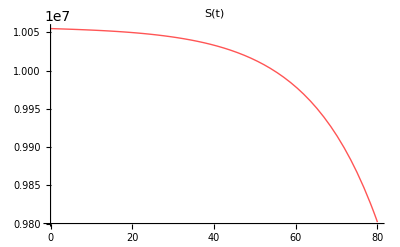

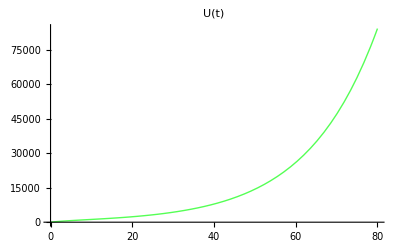

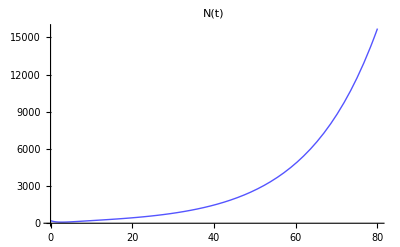

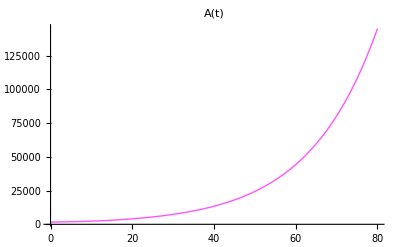

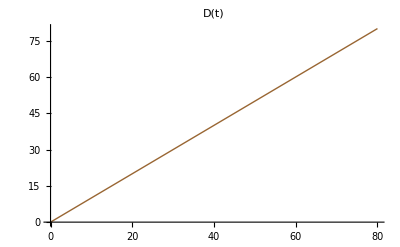

```mathematica
x=0.0611324
p=0.11949
q=0.582564
a=0.00409383
eq= NDSolve[{U'[t]==x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==28,M[0]==208,A[0]==1612,d[0]==1142,S[0]==10054985},{S,U,M,A,d},{t,0,86}]
(*For[i=0,i<87,i++,Print[N[(S[i]/.eq),7]]]*)
(*Plot[{(*U[t]/.eq,S[t]/.eq*),M[t]/.eq,(*A[t]/.eq,d[t]/.eq*)},{t,0,86},PlotRange->All,PlotLegends->"Expressions"]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,*)A[t]/.eq(*,d[t]/.eq*)},{t,0,86},PlotRange->All,PlotLegends->"Expressions"]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,A[t]/.eq,*)d[t]/.eq},{t,0,86},PlotRange->All,PlotLegends->"Expressions"]*)
SetOptions[Plot,BaseStyle->{FontSize->14}];

(*Plot[{(S[t]/(10^3)/.eq),(U[t]/.eq),(M[t]/.eq),(A[t]/.eq),(d[t]/.eq)},{t,0,50},PlotRange->All,PlotLegends->{"S(t)×10^-3","U(t)","N(t)","A(t)","D(t)"},PlotLabel->"Guinea",PlotStyle->{{Lighter[Red],Thick},{Lighter[Green],Thick},{Lighter[Blue],Thick},{Lighter[Magenta],Thick},{Brown,Thick}}]
Plot[{(A[t]/.eq),(d[t]/.eq),(U[t]/.eq)},{t,0,86},PlotRange->All,PlotLegends->{"A(t)", "D(t)", "U(t)"}]
Plot[{(*(M[t]/.eq),*)(S[t]/.eq)},{t,0,159},PlotRange->All,PlotLegends->"S[t]",BaseStyle-> {(*FontWeight->"Bold",*)FontSize->12}]
*)
Plot[{(S[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"S(t)",PlotStyle->{Lighter[Red],Thick}]
Plot[{(U[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"U(t)",PlotStyle->{Lighter[Green],Thick}]
Plot[{(M[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"N(t)",PlotStyle->{Lighter[Blue],Thick}]
Plot[{(A[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"A(t)",PlotStyle->{Lighter[Magenta],Thick}]
Plot[{(D[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"D(t)",PlotStyle->{Brown,Thick}]
```

```mathematica
"
```